```mathematica
Block[{Print},<<xAct`xTras`;<<VariationalMethods`]
$PrePrint=ScreenDollarIndices;
$DefInfoQ=$UndefInfoQ=False;
```

## 基本方程

```mathematica
DefManifold[M,4,IndexRange[a,l]]
DefMetric[-1,metricg[-a,-b],CD,PrintAs->"g"]
```

```mathematica
DefConstantSymbol[κ]
DefTensor[#,M]&/@{ϕ[],A[-a],F[-a,-b]};
DefScalarFunction/@{V,func};
```

```mathematica
IndexSet[F[-a_,-b_],CD[-a]@A[-b]-CD[-b]@A[-a]]
IndexSet[F[a_,b_],metricg[a,c]*metricg[b,d]*F[-c,-d]]
```

▽_a A |  
b-▽_b A |  
a

g | a | c
  |   g | b | d
  |   (▽_c A |  
d-▽_d A |  
c)

```mathematica
DefScalarFunction/@{Ax,φ};
```

```mathematica
(*2*)
DefChart[chartDescartes,M,{0,1,2,3},{t[],x[],y[],z[]}]
DefScalarFunction/@{α,σ};
matrixg={{-1,0,0,0},{0,Exp[2*α[t[]]-4*σ[t[]]],0,0},{0,0,Exp[2*α[t[]]+2*σ[t[]]],0},{0,0,0,Exp[2*α[t[]]+2*σ[t[]]]}};
MetricInBasis[metricg,-chartDescartes,matrixg];
MetricInBasis[metricg,chartDescartes,Inverse[matrixg]];
MetricCompute[metricg,chartDescartes,All,CVSimplify->Simplify,Parallelize->True]
```

```mathematica
ComponentValue[ComponentArray[A[-{a,chartDescartes}]],{0,Ax[t[]],0,0}];
ComponentValue[ComponentArray[A[{a,chartDescartes}]],metricg[{a,chartDescartes},{b,chartDescartes}]*A[-{b,chartDescartes}]//TraceBasisDummy//ComponentArray//ToValues];
ComponentValue[ϕ[],φ[t[]]];
```

Added independent rule A |  
0→0 for tensor A

Added independent rule A |  
1→Ax[t] for tensor A

Added independent rule A |  
2→0 for tensor A

Added independent rule A |  
3→0 for tensor A

Added independent rule A | 0
 →0 for tensor A

Added independent rule A | 1
 →ⅇ^(-2 α[t]+4 σ[t]) Ax[t] for tensor A

Added independent rule A | 2
 →0 for tensor A

Added independent rule A | 3
 →0 for tensor A

Added independent rule ϕ→φ[t] for tensor ϕ

```mathematica
changeIndex=Table[Union[IndexRange[a,l],{l1}][[temp]]->{Union[IndexRange[a,l],{l1}][[temp]],chartDescartes},{temp,1,Length[Union[IndexRange[a,l],{l1}]]}];
```

```mathematica
(*1*)
lagrange=RicciScalarCD[]/(2*κ^2)-1/2*CD[-a]@ϕ[]*CD[a]@ϕ[]-V[ϕ[]]-1/4*func[ϕ[]]^2*F[-a,-b]*F[a,b]
```

R[▽]/(2 κ^2)-V[ϕ]-1/2 (▽_a ϕ) (▽^a ϕ)-1/4 func[ϕ]^2 g | a | c
  |   g | b | d
  |   (▽_a A |  
b-▽_b A |  
a) (▽_c A |  
d-▽_d A |  
c)

#### 先变分再坐标化

```mathematica
eomg=VarL[metricg[a,b],CD][lagrange]//FullSimplification[];
eomA=VarD[A[-a],CD][lagrange*Sqrt[Detmetricg[]]]/Sqrt[Detmetricg[]]//FullSimplification[];
eomϕ=VarD[ϕ[],CD][lagrange*Sqrt[Detmetricg[]]]/Sqrt[Detmetricg[]]//FullSimplification[];
```

```mathematica
ChristoffelCDPDchartDescartes[a,b,-c]//ChristoffelToMetric
```

1/2 g | a | d
  |   g | b | e
  |   (𝒟_c g |   |  
e | d-𝒟_d g |   |  
e | c+𝒟_e g |   |  
c | d)

```mathematica
ChristoffelComponentValue=1/2 {{g, {{a, d}, {, }}}} {{g, {{b, e}, {, }}}} (Subscript[𝒟, c]{{g, {{, }, {e, d}}}}-Subscript[𝒟, d]{{g, {{, }, {e, c}}}}+Subscript[𝒟, e]{{g, {{, }, {c, d}}}})/.changeIndex//TraceBasisDummy//ComponentArray//ToValues// Flatten;
ChristoffelComponent=ChristoffelCDPDchartDescartes[a,b,-c]/.changeIndex// ComponentArray // Flatten;
tempRule=Table[ChristoffelComponent[[n]]->ChristoffelComponentValue[[n]],{n,4^3}];
```

```mathematica
ChangeCovD[#,CD,PD]/.ChristoffelCD->ChristoffelCDPDchartDescartes&/@{eomg,eomA,eomϕ}
```

{(R[▽] |   |  
a | b)/(2 κ^2)-(g |   |  
a | b R[▽])/(4 κ^2)+1/2 g |   |  
a | b V[ϕ]-1/2 func[ϕ]^2 (A | d
  Γ[▽,𝒟] | c |   |  
  | a | d+∂_a A | c
 ) (-A |  
e Γ[▽,𝒟] | e |   |  
  | b | c+∂_b A |  
c)-1/2 ∂_a ϕ ∂_b ϕ+1/2 func[ϕ]^2 (-A |  
d Γ[▽,𝒟] | d |   |  
  | b | c+∂_b A |  
c) (-A |  
e Γ[▽,𝒟] | e | c |  
  |   | a+∂^c A |  
a)-1/2 func[ϕ]^2 (-A |  
d Γ[▽,𝒟] | d |   |  
  | c | b+∂_c A |  
b) (-A |  
e Γ[▽,𝒟] | e | c |  
  |   | a+∂^c A |  
a)+1/2 func[ϕ]^2 (-A |  
d Γ[▽,𝒟] | d |   |  
  | a | c+∂_a A |  
c) (-A |  
e Γ[▽,𝒟] | e | c |  
  |   | b+∂^c A |  
b)+1/4 g |   |  
a | b ∂_c ϕ ∂^c ϕ-1/4 func[ϕ]^2 g |   |  
a | b (-A |  
e Γ[▽,𝒟] | e |   |  
  | c | d+∂_c A |  
d) (A | f
  Γ[▽,𝒟] | c | d |  
  |   | f+∂^d A | c
 )+1/4 func[ϕ]^2 g |   |  
a | b (-A |  
e Γ[▽,𝒟] | e |   |  
  | d | c+∂_d A |  
c) (A | f
  Γ[▽,𝒟] | c | d |  
  |   | f+∂^d A | c
 ),-func[ϕ]^2 (Γ[▽,𝒟] | b |   |  
  | b | e (A | c
  Γ[▽,𝒟] | e | a |  
  |   | c+∂^a A | e
 )+Γ[▽,𝒟] | b | a |  
  |   | c ∂_b A | c
 +A | c
  ∂_b Γ[▽,𝒟] | b | a |  
  |   | c+∂_b ∂^a A | b
 +Γ[▽,𝒟] | a |   |  
  | b | d (A | c
  Γ[▽,𝒟] | b | d |  
  |   | c+∂^d A | b
 ))+func[ϕ]^2 (Γ[▽,𝒟] | a | b |  
  |   | c ∂_b A | c
 +A | c
  ∂_b Γ[▽,𝒟] | a | b |  
  |   | c+∂_b ∂^b A | a
 +Γ[▽,𝒟] | a |   |  
  | b | d (A | c
  Γ[▽,𝒟] | d | b |  
  |   | c+∂^b A | d
 )+Γ[▽,𝒟] | b |   |  
  | b | e (A | c
  Γ[▽,𝒟] | a | e |  
  |   | c+∂^e A | a
 ))-2 func[ϕ] (A | c
  Γ[▽,𝒟] | b | a |  
  |   | c+∂^a A | b
 ) ∂_b ϕ func'[ϕ]+2 func[ϕ] ∂_b ϕ (A | c
  Γ[▽,𝒟] | a | b |  
  |   | c+∂^b A | a
 ) func'[ϕ],∂_a ∂^a ϕ+Γ[▽,𝒟] | a |   |  
  | a | b ∂^b ϕ+func[ϕ] (-A |  
c Γ[▽,𝒟] | c |   |  
  | a | b+∂_a A |  
b) (A | d
  Γ[▽,𝒟] | a | b |  
  |   | d+∂^b A | a
 ) func'[ϕ]-func[ϕ] (-A |  
c Γ[▽,𝒟] | c |   |  
  | b | a+∂_b A |  
a) (A | d
  Γ[▽,𝒟] | a | b |  
  |   | d+∂^b A | a
 ) func'[ϕ]-V'[ϕ]}

```mathematica
{{{R[▽], {{, }, {a, b}}}}/(2 κ^2)-({{g, {{, }, {a, b}}}} R[▽])/(4 κ^2)+1/2 {{g, {{, }, {a, b}}}} V[ϕ]-1/2 func[ϕ]^2 ({{A, {{d}, {}}}} {{Γ[▽,𝒟], {{c, , }, {, a, d}}}}+D[{{A, {{c}, {}}}}, a]) (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, , }, {, b, c}}}}+D[{{A, {{}, {c}}}}, b])-1/2 D[ϕ, a] D[ϕ, b]+1/2 func[ϕ]^2 (-{{A, {{}, {d}}}} {{Γ[▽,𝒟], {{d, , }, {, b, c}}}}+D[{{A, {{}, {c}}}}, b]) (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, c, }, {, , a}}}}+∂^c {{A, {{}, {a}}}})-1/2 func[ϕ]^2 (-{{A, {{}, {d}}}} {{Γ[▽,𝒟], {{d, , }, {, c, b}}}}+D[{{A, {{}, {b}}}}, c]) (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, c, }, {, , a}}}}+∂^c {{A, {{}, {a}}}})+1/2 func[ϕ]^2 (-{{A, {{}, {d}}}} {{Γ[▽,𝒟], {{d, , }, {, a, c}}}}+D[{{A, {{}, {c}}}}, a]) (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, c, }, {, , b}}}}+∂^c {{A, {{}, {b}}}})+1/4 {{g, {{, }, {a, b}}}} D[ϕ, c] ∂^c ϕ-1/4 func[ϕ]^2 {{g, {{, }, {a, b}}}} (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, , }, {, c, d}}}}+D[{{A, {{}, {d}}}}, c]) ({{A, {{f}, {}}}} {{Γ[▽,𝒟], {{c, d, }, {, , f}}}}+∂^d {{A, {{c}, {}}}})+1/4 func[ϕ]^2 {{g, {{, }, {a, b}}}} (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, , }, {, d, c}}}}+D[{{A, {{}, {c}}}}, d]) ({{A, {{f}, {}}}} {{Γ[▽,𝒟], {{c, d, }, {, , f}}}}+∂^d {{A, {{c}, {}}}}),-func[ϕ]^2 ({{Γ[▽,𝒟], {{b, , }, {, b, e}}}} ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{e, a, }, {, , c}}}}+∂^a {{A, {{e}, {}}}})+{{Γ[▽,𝒟], {{b, a, }, {, , c}}}} D[{{A, {{c}, {}}}}, b]+{{A, {{c}, {}}}} D[{{Γ[▽,𝒟], {{b, a, }, {, , c}}}}, b]+∂_b ∂^a {{A, {{b}, {}}}}+{{Γ[▽,𝒟], {{a, , }, {, b, d}}}} ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{b, d, }, {, , c}}}}+∂^d {{A, {{b}, {}}}}))+func[ϕ]^2 ({{Γ[▽,𝒟], {{a, b, }, {, , c}}}} D[{{A, {{c}, {}}}}, b]+{{A, {{c}, {}}}} D[{{Γ[▽,𝒟], {{a, b, }, {, , c}}}}, b]+∂_b ∂^b {{A, {{a}, {}}}}+{{Γ[▽,𝒟], {{a, , }, {, b, d}}}} ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{d, b, }, {, , c}}}}+∂^b {{A, {{d}, {}}}})+{{Γ[▽,𝒟], {{b, , }, {, b, e}}}} ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{a, e, }, {, , c}}}}+∂^e {{A, {{a}, {}}}}))-2 func[ϕ] ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{b, a, }, {, , c}}}}+∂^a {{A, {{b}, {}}}}) D[ϕ, b] func'[ϕ]+2 func[ϕ] D[ϕ, b] ({{A, {{c}, {}}}} {{Γ[▽,𝒟], {{a, b, }, {, , c}}}}+∂^b {{A, {{a}, {}}}}) func'[ϕ],∂_a ∂^a ϕ+{{Γ[▽,𝒟], {{a, , }, {, a, b}}}} ∂^b ϕ+func[ϕ] (-{{A, {{}, {c}}}} {{Γ[▽,𝒟], {{c, , }, {, a, b}}}}+D[{{A, {{}, {b}}}}, a]) ({{A, {{d}, {}}}} {{Γ[▽,𝒟], {{a, b, }, {, , d}}}}+∂^b {{A, {{a}, {}}}}) func'[ϕ]-func[ϕ] (-{{A, {{}, {c}}}} {{Γ[▽,𝒟], {{c, , }, {, b, a}}}}+D[{{A, {{}, {a}}}}, b]) ({{A, {{d}, {}}}} {{Γ[▽,𝒟], {{a, b, }, {, , d}}}}+∂^b {{A, {{a}, {}}}}) func'[ϕ]-V'[ϕ]}/.changeIndex;
Simplify/@ToValues/@ComponentArray/@ToValues/@TraceBasisDummy/@%;
eoms=%/.tempRule;
```

```mathematica
eoms[[1,1;;3]]//Diagonal//FullSimplify//Factor
eoms[[2,2]]//FullSimplify//Factor
eoms[[3]]//FullSimplify//Factor
```

{-(ⅇ^(-2 α[t]) (2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2-6 ⅇ^(2 α[t]) α'[t]^2+6 ⅇ^(2 α[t]) σ'[t]^2+ⅇ^(2 α[t]) κ^2 φ'[t]^2))/(4 κ^2),(ⅇ^(-4 σ[t]) (2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2-6 ⅇ^(2 α[t]) α'[t]^2-12 ⅇ^(2 α[t]) α'[t] σ'[t]-6 ⅇ^(2 α[t]) σ'[t]^2-ⅇ^(2 α[t]) κ^2 φ'[t]^2-4 ⅇ^(2 α[t]) α''[t]-4 ⅇ^(2 α[t]) σ''[t]))/(4 κ^2),-(ⅇ^(2 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+6 ⅇ^(2 α[t]) α'[t]^2-6 ⅇ^(2 α[t]) α'[t] σ'[t]+6 ⅇ^(2 α[t]) σ'[t]^2+ⅇ^(2 α[t]) κ^2 φ'[t]^2+4 ⅇ^(2 α[t]) α''[t]-2 ⅇ^(2 α[t]) σ''[t]))/(4 κ^2)}

-ⅇ^(-2 α[t]+4 σ[t]) func[φ[t]] (func[φ[t]] Ax'[t] α'[t]+4 func[φ[t]] Ax'[t] σ'[t]+2 Ax'[t] func'[φ[t]] φ'[t]+func[φ[t]] Ax''[t])

ⅇ^(-2 α[t]) (ⅇ^(4 σ[t]) func[φ[t]] Ax'[t]^2 func'[φ[t]]-ⅇ^(2 α[t]) V'[φ[t]]-3 ⅇ^(2 α[t]) α'[t] φ'[t]-ⅇ^(2 α[t]) φ''[t])

#### 先坐标化再变分

写出拉格朗日函数的坐标形式，注意加上体元：

```mathematica
ChangeCovD[lagrange,CD,PD]/.ChristoffelCD->ChristoffelCDPDchartDescartes
```

R[▽]/(2 κ^2)-V[ϕ]-1/2 ∂_a ϕ ∂^a ϕ-1/4 func[ϕ]^2 g | a | c
  |   g | b | d
  |   (-A |  
e Γ[▽,𝒟] | e |   |  
  | a | b+A |  
f Γ[▽,𝒟] | f |   |  
  | b | a+∂_a A |  
b-∂_b A |  
a) (-A |  
g Γ[▽,𝒟] | g |   |  
  | c | d+A |  
h Γ[▽,𝒟] | h |   |  
  | d | c+∂_c A |  
d-∂_d A |  
c)

```mathematica
lagrangeC=Sqrt[-DetmetricgchartDescartes[]]*(R[▽]/(2 κ^2)-V[ϕ]-1/2 D[ϕ, a] ∂^a ϕ-1/4 func[ϕ]^2 {{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[▽,𝒟], {{e, , }, {, a, b}}}}+{{A, {{}, {f}}}} {{Γ[▽,𝒟], {{f, , }, {, b, a}}}}+D[{{A, {{}, {b}}}}, a]-D[{{A, {{}, {a}}}}, b]) (-{{A, {{}, {g}}}} {{Γ[▽,𝒟], {{g, , }, {, c, d}}}}+{{A, {{}, {h}}}} {{Γ[▽,𝒟], {{h, , }, {, d, c}}}}+D[{{A, {{}, {d}}}}, c]-D[{{A, {{}, {c}}}}, d]))/.changeIndex//TraceBasisDummy//ToValues//ToValues//Simplify[#,Element[α[t[]],Reals]]&
```

1/2 ⅇ^(3 α[t]) (-2 V[φ[t]]+ⅇ^(-2 α[t]+4 σ[t]) func[φ[t]]^2 Ax'[t]^2+φ'[t]^2+(6 (2 α'[t]^2+σ'[t]^2+α''[t]))/κ^2)

这里使用内置函数进行变分：

```mathematica
VariationalD[lagrangeC,{α[t[]],σ[t[]],Ax[t[]],φ[t[]]},t[]]//FullSimplify//Factor
```

{(ⅇ^α[t] (-6 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+18 ⅇ^(2 α[t]) α'[t]^2+18 ⅇ^(2 α[t]) σ'[t]^2+3 ⅇ^(2 α[t]) κ^2 φ'[t]^2+12 ⅇ^(2 α[t]) α''[t]))/(2 κ^2),(2 ⅇ^α[t] (ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2-9 ⅇ^(2 α[t]) α'[t] σ'[t]-3 ⅇ^(2 α[t]) σ''[t]))/κ^2,-ⅇ^(α[t]+4 σ[t]) func[φ[t]] (func[φ[t]] Ax'[t] α'[t]+4 func[φ[t]] Ax'[t] σ'[t]+2 Ax'[t] func'[φ[t]] φ'[t]+func[φ[t]] Ax''[t]),ⅇ^α[t] (ⅇ^(4 σ[t]) func[φ[t]] Ax'[t]^2 func'[φ[t]]-ⅇ^(2 α[t]) V'[φ[t]]-3 ⅇ^(2 α[t]) α'[t] φ'[t]-ⅇ^(2 α[t]) φ''[t])}

有一个很好解出的方程：

```mathematica
(*3*)
DefConstantSymbol[pA]
ruleAx=D[Ax[t[]],t[]]->func[φ[t[]]]^(-2)*Exp[-α[t[]]-4*σ[t[]]]*pA;
```

将其带入各式，结果如下：

```mathematica
eoms[[1,1;;3]]/.{ruleAx,D[ruleAx,t[]]}//FullSimplify//Diagonal
eoms[[2,2]]/.{ruleAx,D[ruleAx,t[]]}//FullSimplify
eoms[[3]]/.{ruleAx,D[ruleAx,t[]]}//FullSimplify
eom=Join[%%%,{%}];
```

{1/4 (-(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-2 V[φ[t]]+(6 (α'[t]^2-σ'[t]^2))/κ^2-φ'[t]^2),(ⅇ^(-2 (α[t]+4 σ[t])) (pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (-6 (α'[t]+σ'[t])^2+κ^2 (2 V[φ[t]]-φ'[t]^2)-4 (α''[t]+σ''[t]))))/(4 κ^2 func[φ[t]]^2),-(ⅇ^(-2 (α[t]+σ[t])) pA^2)/(4 func[φ[t]]^2)+(ⅇ^(2 (α[t]+σ[t])) (-6 (α'[t]^2-α'[t] σ'[t]+σ'[t]^2)+κ^2 (2 V[φ[t]]-φ'[t]^2)-4 α''[t]+2 σ''[t]))/(4 κ^2)}

0

(ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t]

最终结果

```mathematica
pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0;
pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (κ^2 V[φ[t]]-3 α'[t]^2-α''[t])==0;
(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0;
(ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t]==0;
```

slow-roll inflation

```mathematica
κ^2 V[φ[t]]-3 α'[t]^2==0;
-V'[φ[t]]-3 α'[t] φ'[t]==0;
```

```mathematica
Solve[κ^2 V[φ[t]]-3 α'[t]^2==0,α'[t[]]]
```

{{α'[t]→-(κ √V[φ[t]])/(√3)},{α'[t]→(κ √V[φ[t]])/(√3)}}

```mathematica
Solve[-V'[φ[t]]-3 α'[t] φ'[t]==0,φ'[t[]]]/.{α'[t]->(κ √V[φ[t]])/(√3)}
```

{{φ'[t]→-V'[φ[t]]/(√3 κ √V[φ[t]])}}

```mathematica
α'[t[]]/φ'[t[]]/.{α'[t]->(κ √V[φ[t]])/(√3),φ'[t]->-V'[φ[t]]/(√3 κ √V[φ[t]])}
```

-(κ^2 V[φ[t]])/V'[φ[t]]

-(κ^2 V[φ[t]])/V'[φ[t]]

## 3

```mathematica
DefConstantSymbol/@{m,const};
```

```mathematica
V[φ_]=m^2*φ^2/2;
func[φ_]=Exp[const*κ^2*φ^2/2];
```

```mathematica
eom//.{const->2,κ->1,m->10^(-5)}
```

{1/4 (-ⅇ^(-4 (α[t]+σ[t])-2 φ[t]^2) pA^2-φ[t]^2/10000000000+6 (α'[t]^2-σ'[t]^2)-φ'[t]^2),1/4 ⅇ^(-2 (α[t]+4 σ[t])-2 φ[t]^2) (pA^2+ⅇ^(4 (α[t]+σ[t])+2 φ[t]^2) (φ[t]^2/10000000000-6 (α'[t]+σ'[t])^2-φ'[t]^2-4 (α''[t]+σ''[t]))),-1/4 ⅇ^(-2 (α[t]+σ[t])-2 φ[t]^2) pA^2+1/4 ⅇ^(2 (α[t]+σ[t])) (φ[t]^2/10000000000-6 (α'[t]^2-α'[t] σ'[t]+σ'[t]^2)-φ'[t]^2-4 α''[t]+2 σ''[t]),-φ[t]/10000000000+2 ⅇ^(-4 (α[t]+σ[t])-2 φ[t]^2) pA^2 φ[t]-3 α'[t] φ'[t]-φ''[t]}

```mathematica
Reduce[{1/4 (-ⅇ^(-4 (α[t]+σ[t])-2 φ[t]^2) pA^2-φ[t]^2/10000000000+6 (α'[t]^2-σ'[t]^2)-φ'[t]^2)==0,1/4 ⅇ^(-2 (α[t]+4 σ[t])-2 φ[t]^2) (pA^2+ⅇ^(4 (α[t]+σ[t])+2 φ[t]^2) (φ[t]^2/10000000000-6 (α'[t]+σ'[t])^2-φ'[t]^2-4 (α''[t]+σ''[t])))==0,-1/4 ⅇ^(-2 (α[t]+σ[t])-2 φ[t]^2) pA^2+1/4 ⅇ^(2 (α[t]+σ[t])) (φ[t]^2/10000000000-6 (α'[t]^2-α'[t] σ'[t]+σ'[t]^2)-φ'[t]^2-4 α''[t]+2 σ''[t])==0,-φ[t]/10000000000+2 ⅇ^(-4 (α[t]+σ[t])-2 φ[t]^2) pA^2 φ[t]-3 α'[t] φ'[t]-φ''[t]==0},pA]
```

α''[t]==(φ[t]^2-60000000000 α'[t]^2-30000000000 σ'[t]^2-5000000000 φ'[t]^2)/30000000000&&σ''[t]==(-φ[t]^2+60000000000 α'[t]^2-90000000000 α'[t] σ'[t]-60000000000 σ'[t]^2-10000000000 φ'[t]^2)/30000000000&&φ''[t]==(-φ[t]-2 φ[t]^3+120000000000 φ[t] α'[t]^2-120000000000 φ[t] σ'[t]^2-30000000000 α'[t] φ'[t]-20000000000 φ[t] φ'[t]^2)/10000000000&&(pA==-(ⅈ √(ⅇ^(4 α[t]+4 σ[t]+2 φ[t]^2)) √(φ[t]^2-60000000000 α'[t]^2+60000000000 σ'[t]^2+10000000000 φ'[t]^2))/100000||pA==(ⅈ √(ⅇ^(4 α[t]+4 σ[t]+2 φ[t]^2)) √(φ[t]^2-60000000000 α'[t]^2+60000000000 σ'[t]^2+10000000000 φ'[t]^2))/100000)

```mathematica
sol=NDSolve[{α''[t]==(φ[t]^2-60000000000 α'[t]^2-30000000000 σ'[t]^2-5000000000 φ'[t]^2)/30000000000,σ''[t]==(-φ[t]^2+60000000000 α'[t]^2-90000000000 α'[t] σ'[t]-60000000000 σ'[t]^2-10000000000 φ'[t]^2)/30000000000,φ''[t]==(-φ[t]-2 φ[t]^3+120000000000 φ[t] α'[t]^2-120000000000 φ[t] σ'[t]^2-30000000000 α'[t] φ'[t]-20000000000 φ[t] φ'[t]^2)/10000000000,α[0]==0,α'[0]==0,σ[0]==0,σ'[0]==0,φ[0]==12,φ'[0]==0},{α[t[]],σ[t[]],φ[t[]]},{t[],0,1000}]
```

NDSolve::ndsz: 在 t == 545.917 处，步长实际上为零；可能存在奇点或者刚性系统.

{{α[t]→InterpolatingFunction[…][t],σ[t]→InterpolatingFunction[…][t],φ[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[φ[t[]]/.sol,{t[],0,1000}]
```

-Graphics-

进行一些量纲分析
[α] = [σ] = 1, [m] = [Time]^(-1) = [ϕ] = [κ]^(-1), [pA] = [Time]^(-2)
然后方程(4~7)用 κ 无量纲化如下（一些量的意义已经变化）
t/κ -> t, ϕ κ -> ϕ, m κ ->m, pA κ^2 -> pA
至此方程（带入一些参数后）已经完全可解，但是我不知道 α[t] 和 σ[t] 的初始条件……（难道画 ϕ[t] 的相图不需要这些？）

```mathematica
eoms={D[α[t],t]^2==D[σ[t],t]^2+1/6*D[ϕ[t],t]^2+1/6*m^2*ϕ[t]^2+pA^2/2*Exp[-c*ϕ[t]^2]*Exp[-4*α[t]-4*σ[t]],D[α[t],{t,2}]==-3*D[α[t],t]^2+1/2*m^2*ϕ[t]^2+1/6*pA^2*Exp[-c*ϕ[t]^2]*Exp[-4*α[t]-4*σ[t]],D[σ[t],{t,2}]==-3*D[α[t],t]*D[σ[t],t]+pA^2/3*Exp[-c*ϕ[t]^2]*Exp[-4*α[t]-4*σ[t]],D[ϕ[t],{t,2}]==-3*D[α[t],t]*D[ϕ[t],t]-m^2*ϕ[t]+pA^2*(c*ϕ[t])*Exp[-c*ϕ[t]^2]*Exp[-4*α[t]-4*σ[t]]}
```

{α'[t]^2==1/2 ⅇ^(-4 α[t]-4 σ[t]-c ϕ[t]^2) pA^2+1/6 m^2 ϕ[t]^2+σ'[t]^2+1/6 ϕ'[t]^2,α''[t]==1/6 ⅇ^(-4 α[t]-4 σ[t]-c ϕ[t]^2) pA^2+1/2 m^2 ϕ[t]^2-3 α'[t]^2,σ''[t]==1/3 ⅇ^(-4 α[t]-4 σ[t]-c ϕ[t]^2) pA^2-3 α'[t] σ'[t],ϕ''[t]==-m^2 ϕ[t]+c ⅇ^(-4 α[t]-4 σ[t]-c ϕ[t]^2) pA^2 ϕ[t]-3 α'[t] ϕ'[t]}

```mathematica
Reduce[eoms,pA]
```

α''[t]==1/18 (8 m^2 ϕ[t]^2-48 α'[t]^2-6 σ'[t]^2-ϕ'[t]^2)&&σ''[t]==1/9 (-m^2 ϕ[t]^2+6 α'[t]^2-27 α'[t] σ'[t]-6 σ'[t]^2-ϕ'[t]^2)&&ϕ''[t]==1/3 (-3 m^2 ϕ[t]-c m^2 ϕ[t]^3+6 c ϕ[t] α'[t]^2-6 c ϕ[t] σ'[t]^2-9 α'[t] ϕ'[t]-c ϕ[t] ϕ'[t]^2)&&(pA==-(ⅈ √(ⅇ^(4 α[t]+4 σ[t]+c ϕ[t]^2)) √(m^2 ϕ[t]^2-6 α'[t]^2+6 σ'[t]^2+ϕ'[t]^2))/(√3)||pA==(ⅈ √(ⅇ^(4 α[t]+4 σ[t]+c ϕ[t]^2)) √(m^2 ϕ[t]^2-6 α'[t]^2+6 σ'[t]^2+ϕ'[t]^2))/(√3))

```mathematica
sol=NDSolve[{α''[t]==1/18 (8 m^2 ϕ[t]^2-48 α'[t]^2-6 σ'[t]^2-ϕ'[t]^2),σ''[t]==1/9 (-m^2 ϕ[t]^2+6 α'[t]^2-27 α'[t] σ'[t]-6 σ'[t]^2-ϕ'[t]^2),ϕ''[t]==1/3 (-3 m^2 ϕ[t]-c m^2 ϕ[t]^3+6 c ϕ[t] α'[t]^2-6 c ϕ[t] σ'[t]^2-9 α'[t] ϕ'[t]-c ϕ[t] ϕ'[t]^2),α[0]==0,α'[0]==0,σ[0]==0,σ'[0]==0,ϕ[0]==12,ϕ'[0]==0}/.{c->2,m->10^(-5)},{α[t],σ[t],ϕ[t]},{t,0,2000}];
```

NDSolve::ndsz: 在 t == 1654.04 处，步长实际上为零；可能存在奇点或者刚性系统.

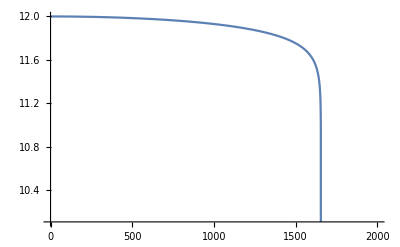

```mathematica
Plot[ϕ[t]/.sol,{t,0,2000}]
```

————————————————————————————————————————————————————————————————上面是后加的。

```mathematica
V[φ[t[]]]=m^2*φ[t[]]^2/2;
func[φ[t[]]]=Exp[c*κ^2*φ[t[]]^2/2];
V'[φ[t[]]]=D[V[φ[t]],φ[t[]]];
func'[φ[t[]]]=D[func[φ[t]],φ[t[]]];
```

```mathematica
{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (κ^2 V[φ[t]]-3 α'[t]^2-α''[t])==0,(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,(ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t]==0}
```

{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (1/2 m^2 κ^2 φ[t]^2-3 α'[t]^2-α''[t])==0,ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,-m^2 φ[t]+c ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2 κ^2 φ[t]-3 α'[t] φ'[t]-φ''[t]==0}

```mathematica
Solve[ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,pA]
```

{{pA→-(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ},{pA→(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ}}

```mathematica
{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (1/2 m^2 κ^2 φ[t]^2-3 α'[t]^2-α''[t])==0,ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,-m^2 φ[t]+c ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2 κ^2 φ[t]-3 α'[t] φ'[t]-φ''[t]==0}/.{pA->(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ}//Simplify
```

{ⅇ^(4 α[t]+4 σ[t]+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t])==0,ⅇ^(4 α[t]+4 σ[t]+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t])==0,True,3 α'[t] φ'[t]+φ[t] (m^2-9 c α'[t] σ'[t]-3 c σ''[t])+φ''[t]==0}

```mathematica
{m^2 κ^2 φ[t]^2-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t]==0,m^2 κ^2 φ[t]^2-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t]==0,3 α'[t] φ'[t]+φ[t] (m^2-9 c α'[t] σ'[t]-3 c σ''[t])+φ''[t]==0}/.{c->2,m->10^-5/κ}
```

{φ[t]^2/10000000000-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t]==0,φ[t]^2/10000000000-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t]==0,3 α'[t] φ'[t]+φ[t] (1/(10000000000 κ^2)-18 α'[t] σ'[t]-6 σ''[t])+φ''[t]==0}

从零开始

```mathematica
V[ϕ[t]]=m^2*ϕ[t]^2/2
f[ϕ[t]]=Exp[2*κ^2*ϕ[t]^2/2]
```

1/2 m^2 ϕ[t]^2

ⅇ^(κ^2 ϕ[t]^2)

```mathematica
{D[α[t],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),D[α[t],{t,2}]==-3*D[α[t],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[σ[t],{t,2}]==-3*D[α[t],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[ϕ[t],{t,2}]==-3*D[α[t],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[t]-4*σ[t]]}//Expand//MatrixForm
```

(α'[t]^2==1/6 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2+1/6 m^2 κ^2 ϕ[t]^2+σ'[t]^2+1/6 κ^2 ϕ'[t]^2
α''[t]==1/6 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2+1/2 m^2 κ^2 ϕ[t]^2-3 α'[t]^2
σ''[t]==1/3 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2-3 α'[t] σ'[t]
ϕ''[t]==-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-3 α'[t] ϕ'[t])

```mathematica
0==D[-D[α[t],t]^2+D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),t]/.{D[α[t],{t,2}]->-3*D[α[t],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[σ[t],{t,2}]->-3*D[α[t],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]}//Simplify
```

3 α'[t] (ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2+m^2 κ^2 ϕ[t]^2+6 σ'[t]^2)+κ^2 ϕ'[t] ((-m^2+2 ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2) ϕ[t]-ϕ''[t])==18 α'[t]^3

```mathematica
Solve[{3 α'[t] (ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2+m^2 κ^2 ϕ[t]^2+6 σ'[t]^2)+κ^2 ϕ'[t] ((-m^2+2 ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2) ϕ[t]-ϕ''[t])==18 α'[t]^3,D[α[t],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),D[ϕ[t],{t,2}]==-3*D[α[t],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[t]-4*σ[t]]},{α'[t],σ'[t],ϕ'[t]}]//MatrixForm
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

(σ'[t]→-(√(-m^4 κ^2 ϕ[t]^2+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) m^2 pA^2 κ^4 ϕ[t]^2-4 ⅇ^(-8 α[t]-8 σ[t]-4 κ^2 ϕ[t]^2) pA^4 κ^6 ϕ[t]^2-9 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 α'[t]^2-9 m^2 κ^2 ϕ[t]^2 α'[t]^2+54 α'[t]^4-2 m^2 κ^2 ϕ[t] ϕ''[t]+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^4 ϕ[t] ϕ''[t]-κ^2 ϕ''[t]^2))/(3 √6 α'[t]) | ϕ'[t]→(-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 α'[t])
σ'[t]→(√(-m^4 κ^2 ϕ[t]^2+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) m^2 pA^2 κ^4 ϕ[t]^2-4 ⅇ^(-8 α[t]-8 σ[t]-4 κ^2 ϕ[t]^2) pA^4 κ^6 ϕ[t]^2-9 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 α'[t]^2-9 m^2 κ^2 ϕ[t]^2 α'[t]^2+54 α'[t]^4-2 m^2 κ^2 ϕ[t] ϕ''[t]+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^4 ϕ[t] ϕ''[t]-κ^2 ϕ''[t]^2))/(3 √6 α'[t]) | ϕ'[t]→(-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 α'[t]))

```mathematica
DSolve[{ϕ'[t]==(-m^2 ϕ[t]+2 ⅇ^(-4 α-4 σ-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 a),ϕ[0]==12,ϕ'[0]==0},ϕ[t],t]
```

$Aborted

尝试使用 (10)

```mathematica
V[ϕ[t]]=m^2*ϕ[t]^2/2
f[ϕ[t]]=Exp[c*κ^2*ϕ[t]^2/2]
α[ϕ[t]]=-(c*κ^2*ϕ[t]^2)/4
```

1/2 m^2 ϕ[t]^2

ⅇ^(1/2 c κ^2 ϕ[t]^2)

-1/4 c κ^2 ϕ[t]^2

```mathematica
Solve[{D[α[ϕ[t]],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]]),D[α[ϕ[t]],{t,2}]==-3*D[α[ϕ[t]],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]],D[σ[t],{t,2}]==-3*D[α[ϕ[t]],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]],D[ϕ[t],{t,2}]==-3*D[α[ϕ[t]],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[ϕ[t]]-4*σ[t]]}/.{c->2,m->10^(-5)/κ},{σ[t],σ'[t],σ''[t],ϕ'[t]}][[1]][[3]]
```

ϕ'[t]→-(√(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t]))/(√(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3))

```mathematica
ϕ'[t]^2==(-(√(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t]))/(√(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3)))^2
```

```mathematica
ϕ'[t]^2==(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t])/(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3)/.{κ->1,ϕ[t]->x,ϕ'[t]->v[x],ϕ''[t]->(v[x]*D[v[x],x])}
```

v[x]^2==(x+6 x^3+10000000000 v[x] v'[x]+120000000000 x^2 v[x] v'[x])/(-90000000000 x+360000000000 x^3)

```mathematica
s=NDSolve[{(-90000000000 x+360000000000 x^3)*v[x]^2==x+6 x^3+10000000000 v[x] v'[x]+120000000000 x^2 v[x] v'[x],v[12]==0.0001},{v[x]},{x,0,12}]
```

{{v[x]→InterpolatingFunction[…][x]}}

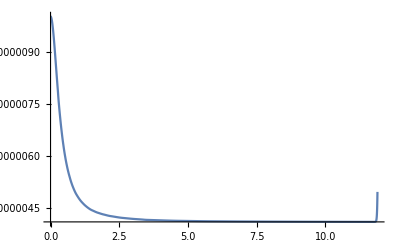

```mathematica
Plot[Evaluate[v[x]/.s],{x,0,11.9},PlotRange->All]
```